```mathematica
Quit[]
ClearAll;
```

```mathematica
(*This mathematica script produces all the plots on figures 8 and 9 of arXiv:2306.03893.*)
(*NB: All the equation numbers come from arXiv:2306.03893*)
(*NB: These scripts produces some computational errors. These are because of the breakdown of numercial methods (e.g. NIntegrate) in the unphysical region and the lack of precise test to exclude them. Therrefore, it does not influence the physical results of the paper.*)
```

## Negative λ0 Scan

```mathematica
(*Script for the negative λ0: reproduces the datats for the 4 panels of figure 9.*)
(*I. Definitions*)
```

```mathematica
ξlow =0.20927 - 0.001; ξup =00.20927+ 0.001; Size =60;(*Scan Range/Size*)
xi[p1_]:= ξlow + (ξup-ξlow)p1/Size;
(*Table where we will put all the values of the scan*)
Dat = {}; CMB = {}; Lam = {}; Ratio = {}; Spect = {}; Init = {};
Clear[λ0,q,b];
(*These parameters come from a script written by Fedor Bezrukov. This computes the running of the Standard Model coupling using the MS-Bar Scheme. It uses 2 loop matching of physical and MS-Bar parameters and 3 loop evolution of the coupling constants. As an input, it uses Subscript[α, s][Subscript[M, Z]] = 0.1181 and Subscript[m, h] = 125.1 GeV. It also neglected the running of ξ.*)
FitParam ={mt0->172.76,Yt0->0.9338148657541936,λ0->-0.012267716676254729,b->0.00002844665271177031,q->0.2545115831381372};
λ0 = λ0/.FitParam[[3]]; b = b/.FitParam[[4]]; q = q/.FitParam[[5]];yt = 0.42733042003306865;
(*Functions of the theory*)
F[x1_,ξ1_]= 1/Sqrt[ξ1] Tanh[Sqrt[ξ1]x1];(*Palatini F, eq (3.11)*)
λSM[μ1_]= λ0 + b Log[μ1/q]^2;(*Sm Running Without UV as function of the scale μ, eq (3.22)*)
μ[x1_,ξ1_]= yt F[x1,ξ1];(*Energy Scale as the top mass eq (3.26)*)
G[x1_,ξ1_]=(D[F[x1,ξ1],x1])^2 + 1/3(D[D[F[x1,ξ1],x1],x1])F[x1,ξ1];(*Definition of the jump in the coupling constant according to 1412.3811, eq (3.29)*)
λ[x1_,ξ1_,δλ1_]= λSM[μ[x1,ξ1]]+ δλ1(1-G[x1,ξ1]^2);(*UV Running, eq (3.28)*)
U[x1_,ξ1_,δλ1_]= 1/4 λ[x1,ξ1,δλ1]F[x1,ξ1]^4;(*Full Potential, eq (3.31)*)
dU[x1_,ξ1_,δλ1_]=( D[U[x1,ξ1,δλ1],x1]);(*We take the derivative of the potential in order to use it later.*)
ϵSR[x1_,ξ1_,δλ1_]= 1/2(dU[x1,ξ1,δλ1]/U[x1,ξ1,δλ1])^2;(*Slow roll parameter in order to define initial conditions for the velocity as function of the initial condition.*)
δλmin[ξ1_]=-λ0-b Log[yt/(q Sqrt[ξ1])]^2 ;(*Minimal value of the jump such that the potential and its derivative stay positive at large field, eq (4.30)*)
(*II. Scan over ξ.*)
For[p=Size,p>=0, p--, ξ = xi[p];
(*II.A. According to the procedure described in section 4.2.2, we find the allowed interval for δλ at given ξ.*)
(*II.A.1. We find the upper bound δλplus*)
δup = Abs[λ0]; δlow = δλmin[ξ]/1000; Nstep = 30;
Module[{δ,dUTab,Rank,Test,Firs},
Pos = False;
Firs = 0;
For[i=1,i<=Nstep,i++, 
δ = δlow (δup/δlow)^((i-1)/(Nstep-1));
δλ = δλmin[ξ]+δ;
dUTab = Table[{x,dU[x,ξ,δλ]},{x,$MachineEpsilon,4/Sqrt[ξ],0.01/Sqrt[ξ]}];
Rank = {};
Test = Sign[dUTab[[1]][[2]]];
For[j=1,j<=Length[dUTab],j++,
If[Test != Sign[dUTab[[j]][[2]]],AppendTo[Rank,j]];
Test = Sign[dUTab[[j]][[2]]];
];
If[U[dUTab[[Rank[[Length[Rank]]]]][[1]],ξ,δλ]>0,Pos = True];
If[Firs == 0, If[Length[Rank]!=4, R = i; Firs = 1]];

];
δplus = δlow (δup/δlow)^((R-1)/(Nstep-1));];
δλplus = δλmin[ξ]+δplus;
(*II.A.2 We find the lower bound δλminus*)
(*NB: Sometimes, at δλplus, the almost inflection point is still negative. In these cases, there is no way to find a local min in the potential. Hence, the program sets Pos==False which stops the loop on p.*)
If[Pos == True,δup = δplus; δlow = 10^(-6)δλmin[ξ]; Nstep = 50;
Module[{Rank2,δ,dUTab,Rank,Test,ULocMin,Neg},
Rank2 = {};
For[i=1,i<=Nstep,i++, 
δ = δlow (δup/δlow)^((i-1)/(Nstep-1));
δλ = δλmin[ξ]+δ;
dUTab = Table[{x,dU[x,ξ,δλ]},{x,$MachineEpsilon,4/Sqrt[ξ],0.01/Sqrt[ξ]}];
Rank = {};
Test = Sign[dUTab[[1]][[2]]];
For[j=1,j<=Length[dUTab],j++,
If[Test != Sign[dUTab[[j]][[2]]],AppendTo[Rank,j]];
Test = Sign[dUTab[[j]][[2]]];
];
ULocMin = U[dUTab[[Rank[[Length[Rank]]]]][[1]],ξ,δλ];
If[ULocMin >=0, Neg = False,Neg = True];
If[Neg == False,AppendTo[Rank2,i]]
];
δminus  = δlow (δup/δlow)^(Rank2[[1]]/Nstep);
δλminus =δλmin[ξ]+δminus;],Break[](*Stops the scan if Pos==False because we reach the lower bound on ξ.*)];
ClearAll[δλ];
(*II.B. Scan Over δλ € [δλminus,δλplus] in order to find the minimal initial power spectrum.*)
nSize = 100;
δλ[n1_]= δλminus + n1/nSize(δλplus - δλminus)(*Parametrizes the Jump between the two bounds. n =100 corresponds to the smallest loc min and 0 to the largest.*);
(*Finds the largest n such that the inflation is still ending somewhere*)
Fin = True;Stable = True;Hilltop = False; n=nSize; L = 1000/Sqrt[ξ]; χi = 4/Sqrt[ξ]; PCMBn = {};
While[Fin == True && n>=0 && Hilltop == False && Stable == True,
dχi = -Sqrt[2ϵSR[χi,ξ,δλ[n]]];
χsol =NDSolveValue[{y''[Ne] + 3 y'[Ne] -1/2 (y'[Ne])^3 + (3-1/2(y'[Ne])^2)dU[y[Ne],ξ,δλ[n]]/U[y[Ne],ξ,δλ[n]]==0,y[0]==χi, y'[0]==dχi},y,{Ne,$MachineEpsilon,L}];
Nup = ResourceFunction["InterpolatingFunctionDomain"][χsol][[1]][[2]];
ϵ[x1_]= 1/2(χsol'[x1])^2;
H[x1_]=Sqrt[U[χsol[x1],ξ,δλ[n]]/(6-(χsol'[x1])^2)];
If[Max[Table[Re[ϵ[x]],{x,0,Nup,Nup/10000}]]>=1,
Fin = True;,(*Inflation comes to an end for this value of n.*)
Fin = False; nMin = n+1(*Inflation does not come to an end for this n, the minimal n in n+1..*);];
(*If the inflation does not ends for the largest n, this is not a good value of ξ to consider.*)
If[Fin==False && n==nSize,NoInf=True,NoInf=False];
If[Fin==True, (*When Inflation is ending, it happens sometimes that the inflation begins at the left of the local maximum, preventing the system to go through the required USR phase. The aim of this test is to avoid these cases.*)
(*a) We find the value of Nend and NCMB.*)
If[Nup == L,Nup1 = Nup;
For[i=2,i<10,i++, Nup1 = Nup/i;
If[Abs[Im[ϵ[Nup1]]]== 0,Nup1 = Nup/(i-1);Break[];];
]; If[ϵ[Nup/i]<1,Ninf = Nup /i,Ninf = Nup1/2];
, Ninf = Nup/2; Nup1 = Nup;];
T =Table[{ϵ[x]-1,x},{x,Ninf,Nup1,(Nup1-Ninf)/30000}];
Laste = False;
For[a =1, a<=Length[T]-1, a++, 
If[Laste == False,If[Sign[T[[a]][[1]]]!= Sign[T[[a+1]][[1]]],A = a; Laste = True]]
];
Nend = T[[A]][[2]];
NCMB = Nend-55;
(*b) We find the location of the local maximum, i.e. the first time that the derivative chanhge its sign.*)
dUTab = Table[{dU[x,ξ,δλ[n]],x},{x,0.2/Sqrt[ξ],1/Sqrt[ξ],0.01/Sqrt[ξ]}];
Passed = False;
For[k = 1,k<=Length[dUTab]-1,k++, 
If[Sign[dUTab[[k]][[1]]]!= Sign[dUTab[[k+1]][[1]]],Passed = True; χex = dUTab[[k]][[2]];Break[]];
];
If[Passed == False, 
MinDer = Min[ Table[{dU[x,ξ,δλ[n]]},{x,0.2/Sqrt[ξ],1/Sqrt[ξ],0.01/Sqrt[ξ]}]];
For[k = 1,k<=Length[dUTab]-1,k++, 
If[dUTab[[k]][[1]]==MinDer, χex = dUTab[[k]][[2]]]
];
];
(*c. Now we compare a and b.*)
If[Re[χsol[NCMB]]<= χex,Hilltop = True; nMin = n+1;,Hilltop = False;];
];
(*If Hilltop = True at n=nSize, this mean that it is an unavoidable scenario for these (λ0,ξ)*)
If[Hilltop==True && n==nSize, NoInf==True;,NoInf==False;];
If[Fin == True && Hilltop == False,
χStable = Interpolation[Table[{U[x,ξ,δλ[n]],x},{x,0.5/Sqrt[ξ],4/Sqrt[ξ],0.01/Sqrt[ξ]}]][0];
(*If the previous test is concluding, we still have to make a stability test due to the negative λ0*)
If[χsol[Nend]<=χStable, Stable = False; nMin = n+1; , Stable = True; PCMBSR = H[NCMB]^2/(8 Pi^2 ϵ[NCMB]); AppendTo[PCMBn,{n,PCMBSR}]; n = n-1;];
If[Stable ==False && n==100, NoInf == True;,NoInf==False];
];
];
(*End of the scan over the jump.*)
If[n==100,If[Fin==False,NoInf = True;,NoInf = False;],NoInf=False;]
(*II.C. We select the minimal CMB*);
PCMBnValues ={};
For[i=1,i<=Length[PCMBn], i++, AppendTo[PCMBnValues,{PCMBn[[i]][[2]]}]];
CMBnMin = Min[PCMBnValues];ClearAll[PCMBnValues];
For[i=1, i<=Length[PCMBn], i++,If[PCMBn[[i]][[2]]==CMBnMin, Rankn = i]];
nMinCMB = PCMBn[[Rankn]][[1]];
(*We re do the background analysis for the minimal CMB*)
If[NoInf==False,
n = nMinCMB;
dχi = -Sqrt[2ϵSR[χi,ξ,δλ[n]]];
χsol =NDSolveValue[{y''[Ne] + 3 y'[Ne] -1/2 (y'[Ne])^3 + (3-1/2(y'[Ne])^2)dU[y[Ne],ξ,δλ[n]]/U[y[Ne],ξ,δλ[n]]==0,y[0]==χi, y'[0]==dχi},y,{Ne,$MachineEpsilon,L}];
Nup = ResourceFunction["InterpolatingFunctionDomain"][χsol][[1]][[2]];
ϵ[x1_]= 1/2(χsol'[x1])^2;
H[x1_]=Sqrt[U[χsol[x1],ξ,δλ[n]]/(6-(χsol'[x1])^2)];
If[Nup == L,Nup1 = Nup;
For[i=2,i<10,i++, Nup1 = Nup/i;
If[Abs[Im[ϵ[Nup1]]]== 0,Nup1 = Nup/(i-1);Break[];];
]; If[ϵ[Nup/i]<1,Ninf = Nup /i,Ninf = Nup1/2];
, Ninf = Nup/2; Nup1 = Nup;];
T =Table[{ϵ[x]-1,x},{x,Ninf,Nup1,(Nup1-Ninf)/30000}];
Laste = False;
For[a =1, a<=Length[T]-1, a++, 
If[Laste == False,If[Sign[T[[a]][[1]]]!= Sign[T[[a+1]][[1]]],A = a; Laste = True]]
];
Nend = T[[A]][[2]];
NCMB = Nend-55;
Pζ[Nfold_]= H[Nfold]^2/(8 Pi^2 ϵ[Nfold]);
Enh =Log10[ Max[Table[Pζ[x],{x,NCMB,Nend,0.1}]]/Pζ[NCMB]];
ηCMB =(D[dU[x,ξ,δλ[n]],x]/.x->χsol[NCMB])/U[χsol[NCMB],ξ,δλ[n]];
ϵCMB = ϵ[χsol[NCMB]];
ns = 1-2ϵCMB -ηCMB;
(*ns_PLANCK = 0.9603±0.0073*)
r = 16ϵCMB;
(*PCMB_PLANCK = 2.1*^-9*)
AppendTo[Dat,{ξ,Enh}];
AppendTo[CMB,{ξ,Pζ[NCMB]}];
AppendTo[Spect,{ξ,ns}];
AppendTo[Ratio,{ξ,r}];
AppendTo[Lam,{ξ,δλ[n]}];
AppendTo[Init,{ξ,χsol[NCMB]}];
](*End of If for NoInf*);
](*End of II., i.e. the scan over ξ for negative λ0*)
(*III. We complete the analysis by the computation of the exact CMB power specrum by making use of the Mukhanov Sasaki equation.*)
ExCMB = {};
For[i=1, i<=Length[CMB],i++,
ξ = CMB[[i]][[1]]; δλ = Lam[[i]][[2]]; χi = 4/Sqrt[ξ]; L = 1000/Sqrt[ξ];
dχi = -Sqrt[2ϵSR[χi,ξ,δλ]];
χsol =NDSolveValue[{y''[Ne] + 3 y'[Ne] -1/2 (y'[Ne])^3 + (3-1/2(y'[Ne])^2)dU[y[Ne],ξ,δλ]/U[y[Ne],ξ,δλ]==0,y[0]==χi, y'[0]==dχi},y,{Ne,$MachineEpsilon,L}];
Nup = ResourceFunction["InterpolatingFunctionDomain"][χsol][[1]][[2]];
ϵ[x1_]= 1/2(χsol'[x1])^2;
H[x1_]=Sqrt[U[χsol[x1],ξ,δλ]/(6-(χsol'[x1])^2)];
Δ = Abs[Nup -55];
T =If[Δ < 5, Table[{ϵ[x]-1,x},{x,Nup-Δ,Nup,0.001}],Table[{ϵ[x]-1,x},{x,Nup-Δ,Nup,0.005}]];
Laste = False;
For[a =1, a<=Length[T]-1, a++, 
If[Laste == False,If[Sign[T[[a]][[1]]]!= Sign[T[[a+1]][[1]]],A = a; Laste = True]]
];
Nend = T[[A]][[2]];
NCMB = Nend-55;

L1 = 100;
kcross[Nfold_]= 0.05/H[NCMB] H[Nfold]E^(Nfold-NCMB);
Ncross = Interpolation[Table[{Re[kcross[x]],x},{x,NCMB-10,Nend,(Nend-NCMB+10)/10000}]];
k = kcross[NCMB];
ki = k/L1;(*we define some scale that crosses the Hubble radius when k is still in the BD vacuum. Here, ki crosses 1 efold before the CMB.*)
Ni = Ncross[ki];(*Initial time for Mukhanov Sasaki intergation*)
fin = 1/Sqrt[2 k] Exp[-I k/ki];
dfin =- (I Sqrt[k/2])/ki Exp[-I k/ki];
η[Nfold_]= ϵ[Nfold]-1/2 ϵ'[Nfold]/ϵ[Nfold];
fsol = NDSolveValue[{y''[x] + (1-ϵ[x])y'[x] + (k^2/kcross[x]^2+(1+ϵ[x]-η[x])(η[x]-2)-(ϵ'[x]-η'[x]))y[x]==0, y[Ni]== fin, y'[Ni]==dfin},y,{x,Ni,Nend}];
Nup = ResourceFunction["InterpolatingFunctionDomain"][fsol][[1]][[2]];
z[Nfold_]=-0.05/H[NCMB] E^(Nfold-NCMB)χsol'[Nfold];
Modsq[z1_]= Re[z1]^2 + Im[z1]^2;
Pow[Nfold_] = k^3/(2 Pi^2)Modsq[fsol[Nfold]/z[Nfold]];
AppendTo[ExCMB,{ξ,Pow[Nup]}];
]
(*Finds the Minimal CMB for both MS and SR methods.*)
CMBValues = {};
For[i=1,i<=Length[CMB],i++, AppendTo[CMBValues,CMB[[i]][[2]]]];
MinCMBValues = Min[CMBValues];
For[i=1,i<=Length[CMB],i++,If[CMB[[i]][[2]]==MinCMBValues, Rank=i;]];
ξ = CMB[[Rank]][[1]];
ExCMBValues = {};
For[i=1,i<=Length[ExCMB],i++, AppendTo[ExCMBValues,ExCMB[[i]][[2]]]];
MinExCMBValues = Min[ExCMBValues];
For[i=1,i<=Length[ExCMB],i++,If[ExCMB[[i]][[2]]==MinExCMBValues, ExRank=i;]];
ξEx = CMB[[ExRank]][[1]];
plot2 = ListLogPlot[ExCMB,PlotStyle->Orange,PlotRange->All];
plot1 = ListLogPlot[CMB,PlotRange->All];
```

## Positive λ0 Scan

```mathematica
(*Script for the negative λ0: reproduces the datas for the 4 panels of figure 8.*)
(*I. Definitions*)
ξlow=0.0936; ξup=0.0956; Size =100;(*Scan Range/Size*)
xi[p1_]:= ξlow + (ξup-ξlow)p1/Size;
Dat = {}; CMB = {}; Lam = {}; Ratio = {}; Spect = {}; Init = {};(*Table where we will put all the values of the scan*)
Clear[λ0,q,b];
(*These parameters come from a script written by Fedor Bezrukov. This computes the running of the Standard Model coupling using the MS-Bar Scheme. It uses 2 loop matching of physical and MS-Bar parameters and 3 loop evolution of the coupling constants. As an input, it uses Subscript[α, s][Subscript[M, Z]] = 0.1181 and Subscript[m, h] = 125.1 GeV. It also neglected the running of ξ. The paticular value here corresponds to yt0 = 0.919 in digure 8.*)
FitParam ={mt0->170.25,Yt0->0.9191638473923207,λ0->0.00395130850979683,b->0.00002273980608174033,q->0.34337846047769355};
λ0 = λ0/.FitParam[[3]]; b = b/.FitParam[[4]]; q = q/.FitParam[[5]];yt = 0.42733042003306865;
(*Functions of the theory*)
F[x1_,ξ1_]= 1/Sqrt[ξ1] Tanh[Sqrt[ξ1]x1];(*Palatini F, eq (3.11)*)
λSM[μ1_]= λ0 + b Log[μ1/q]^2;(*Sm Running Without UV as function of the scale μ, eq (3.22)*)
μ[x1_,ξ1_]= yt F[x1,ξ1];(*Energy Scale as the top mass eq (3.26)*)
G[x1_,ξ1_]=(D[F[x1,ξ1],x1])^2 + 1/3(D[D[F[x1,ξ1],x1],x1])F[x1,ξ1];(*Definition of the jump function according to 1412.3811 paper, eq (3.30)*)
λ[x1_,ξ1_,δλ1_]= λSM[μ[x1,ξ1]]+ δλ1(1-G[x1,ξ1]^2);(*UV Running, eq (3.28)*)
U[x1_,ξ1_,δλ1_]= 1/4 λ[x1,ξ1,δλ1]F[x1,ξ1]^4;(*Full Potential, eq (3.31)*)
dU[x1_,ξ1_,δλ1_]=( D[U[x1,ξ1,δλ1],x1]);(*We take the derivative of the potential in order to use it later.*)
ϵSR[x1_,ξ1_,δλ1_]= 1/2(dU[x1,ξ1,δλ1]/U[x1,ξ1,δλ1])^2;(*Slow roll parameter in order to define initial conditions for the velocity.*)
δλmin[ξ1_]=-λ0-b Log[yt/(q Sqrt[ξ1])]^2 ;(*Minimal value of the jump such that the potential and its derivative stay positive at large field, eq (4.33)*)
(*II. Scan over ξ*)
For[p=Size, p>=0, p--, ξ = xi[p];
(*II.A. According to the procedure described in section 4.2.2, we find the allowed interval for δλ at given ξ.*)
(*II.A.1. We find the upper bound δλplus*)
δup = λ0+0.0001; δlow = Abs[δλmin[ξ]]/1000; Nstep = 30;
Pos = False;
Firs = 0;
For[i=1,i<=Nstep,i++, 
δ = δlow (δup/δlow)^((i-1)/(Nstep-1));
δλ = δλmin[ξ]+δ;
dUTab = Table[{x,dU[x,ξ,δλ]},{x,$MachineEpsilon,4/Sqrt[ξ],0.01/Sqrt[ξ]}];
Rank = {};
Test = Sign[dUTab[[1]][[2]]];
For[j=1,j<=Length[dUTab],j++,
If[Test != Sign[dUTab[[j]][[2]]],AppendTo[Rank,j]];
Test = Sign[dUTab[[j]][[2]]];
];
L = Length[Rank];
If[L!=0,If[U[dUTab[[Rank[[L]]]][[1]],ξ,δλ]>0,Pos = True]];
If[Firs == 0, If[L==0, R = i; Firs = 1]];

];
δplus = δlow (δup/δlow)^((R-1)/(Nstep-1));
δλplus = δλmin[ξ]+δplus;
(*II.A.2 We find the lower bound δλminus*)
Nstep = 30;
Test = False;
n = 1;
While[Test ==False && n<=Nstep,
δminus = δlow (δplus/δlow)^((n-1)/(Nstep-1));
δλ = δλmin[ξ]+δminus;
TU = Table[U[x,ξ,δλ],{x,$MachineEpsilon,4/Sqrt[ξ],0.01}];
TX = Table[x,{x,$MachineEpsilon,4/Sqrt[ξ],0.01}];
MaxU = Max[TU];
If[MaxU==U[ TX[[Length[TX]]],ξ,δλ],Test = True, Test = False];
n= n+1;
](*PositiveNess*);
If[Min[TU]<0,Pos = False;,Pos = True;];
n = 1;
Firs = 0;
δmin = δminus;
While[Pos == False && n<=Nstep,
δ = δmin(δplus/δmin)^((n-1)/(Nstep-1));
δλ =  δλmin[ξ]+δ;
TU = Table[U[x,ξ,δλ],{x,$MachineEpsilon,4/Sqrt[ξ],0.01}];
If[Min[TU]>0,Pos = True];
If[Firs==0, If[Pos==True,δminus = δ; Firs=1]];
n=n+1
];
δλminus = δλ;
ClearAll[δλ];
(*II.B. Scan Over δλ € [δλminus,δλplus] in order to find the minimal initial power spectrum.*)
nSize = 100;
δλ[n1_]= δλminus + n1/nSize(δλplus - δλminus)(*Parametrizes the Jump between the two bounds. n =100 corresponds to the smallest loc min and 0 to the largest.*);
(*Finds the largest n such that the inflation is still ending somewhere*)
Fin = True;Hilltop = False; n=nSize; L = 1000/Sqrt[ξ]; χi = 4/Sqrt[ξ]; PCMBn = {};NoInf=False;
While[Fin == True && n>=0 && Hilltop == False,
dχi = -Sqrt[2ϵSR[χi,ξ,δλ[n]]];
χsol =NDSolveValue[{y''[Ne] + 3 y'[Ne] -1/2 (y'[Ne])^3 + (3-1/2(y'[Ne])^2)dU[y[Ne],ξ,δλ[n]]/U[y[Ne],ξ,δλ[n]]==0,y[0]==χi, y'[0]==dχi},y,{Ne,$MachineEpsilon,L}];
Nup = ResourceFunction["InterpolatingFunctionDomain"][χsol][[1]][[2]];
ϵ[x1_]= 1/2(χsol'[x1])^2;
H[x1_]=Sqrt[U[χsol[x1],ξ,δλ[n]]/(6-(χsol'[x1])^2)];
If[Max[Table[Re[ϵ[x]],{x,0,Nup,Nup/10000}]]>=1,
Fin = True;,(*Inflation comes to an end for this value of n.*)
Fin = False; nMin = n+1(*Inflation does not come to an end for this n, the minimal n in n+1..*);If[n==nSize, NoInf=True;](*If the inflation does not ends for the largest n, this is not a good value of ξ to consider.*);];
(*When Inflation is ending, it happens sometimes that the inflation begins at the left of the local maximum, preventing the system to go through the required USR phase. The aim of this test is to avoid these cases.*)
(*a) We find the value of Nend and NCMB.*)
If[Fin==True,
Ninf = 0;
If[Nup == L,Nup1 = Nup;
For[i=2,i<10,i++, Nup1 = Nup/i;
If[Abs[Im[ϵ[Nup1]]]== 0,Nup1 = Nup/(i-1);Break[];];
]; ,Nup1 = Nup;];
T =Table[{ϵ[x]-1,x},{x,Ninf,Nup1,(Nup1-Ninf)/30000}];
Laste = False;
For[a =1, a<=Length[T]-1, a++, 
If[Laste == False,If[Sign[T[[a]][[1]]]!= Sign[T[[a+1]][[1]]],A = a; Laste = True]]
];
Nend = T[[A]][[2]];
NCMB = Nend-55;
(*b) We find the location of the local maximum, i.e. the first time that the derivative chanhge its sign.*)
dUTab = Table[{dU[x,ξ,δλ[n]],x},{x,0.2/Sqrt[ξ],1/Sqrt[ξ],0.01/Sqrt[ξ]}];
Passed = False;
For[k = 1,k<=Length[dUTab]-1,k++, 
If[Sign[dUTab[[k]][[1]]]!= Sign[dUTab[[k+1]][[1]]],Passed = True; χex = dUTab[[k]][[2]];Break[]];
];
If[Passed == False, 
MinDer = Min[ Table[{dU[x,ξ,δλ[n]]},{x,0.2/Sqrt[ξ],1/Sqrt[ξ],0.01/Sqrt[ξ]}]];
For[k = 1,k<=Length[dUTab]-1,k++, 
If[dUTab[[k]][[1]]==MinDer, χex = dUTab[[k]][[2]]]
];
];
(*c. Now we compare a and b.*)
If[Re[χsol[NCMB]]<= χex,Hilltop = True; nMin = n+1; If[n==nSize, NoInf==True(*If Hilltop = True at n=nSize, this mean that it is an unavoidable scenario for these (λ0,ξ)*);],Hilltop = False;  AppendTo[PCMBn,{n,H[NCMB]^2/(8 Pi^2 ϵ[NCMB])}];(*We keep the SR CMB in memeory for each n.*)n = n-1;];];
](*End of the scan over δλ*);
(*We select the minimal CMB and we make all the standard dynamics.*)
PCMBnValues ={};
For[i=1,i<=Length[PCMBn], i++, AppendTo[PCMBnValues,{PCMBn[[i]][[2]]}]];
CMBnMin = Min[PCMBnValues];ClearAll[PCMBnValues];
For[i=1, i<=Length[PCMBn], i++,If[PCMBn[[i]][[2]]==CMBnMin, Rankn = i]];
nMinCMB = PCMBn[[Rankn]][[1]];
(*We re do the analysis for the minimal CMB*)
If[NoInf==False,
n = nMinCMB;
dχi = -Sqrt[2ϵSR[χi,ξ,δλ[n]]];
χsol =NDSolveValue[{y''[Ne] + 3 y'[Ne] -1/2 (y'[Ne])^3 + (3-1/2(y'[Ne])^2)dU[y[Ne],ξ,δλ[n]]/U[y[Ne],ξ,δλ[n]]==0,y[0]==χi, y'[0]==dχi},y,{Ne,$MachineEpsilon,L}];
Nup = ResourceFunction["InterpolatingFunctionDomain"][χsol][[1]][[2]];
ϵ[x1_]= 1/2(χsol'[x1])^2;
H[x1_]=Sqrt[U[χsol[x1],ξ,δλ[n]]/(6-(χsol'[x1])^2)];
Ninf = 0;
If[Nup == L,Nup1 = Nup;
For[i=2,i<10,i++, Nup1 = Nup/i;
If[Abs[Im[ϵ[Nup1]]]== 0,Nup1 = Nup/(i-1);Break[];];
]; ,Nup1 = Nup;];
T =Table[{ϵ[x]-1,x},{x,Ninf,Nup1,(Nup1-Ninf)/30000}];
Laste = False;
For[a =1, a<=Length[T]-1, a++, 
If[Laste == False,If[Sign[T[[a]][[1]]]!= Sign[T[[a+1]][[1]]],A = a; Laste = True]]
];
Nend = T[[A]][[2]];
NCMB = Nend-55;
Pζ[Nfold_]= H[Nfold]^2/(8 Pi^2 ϵ[Nfold]);
Enh =Log10[ Max[Table[Pζ[x],{x,NCMB,Nend,0.1}]]/Pζ[NCMB]];
ηCMB =(D[dU[x,ξ,δλ[n]],x]/.x->χsol[NCMB])/U[χsol[NCMB],ξ,δλ[n]];
ϵCMB = ϵ[χsol[NCMB]];
ns = 1-6ϵCMB +2ηCMB;
(*ns_PLANCK = 0.9603±0.0073*)
r = 16ϵCMB;
(*PCMB_PLANCK = 2.1*^-9*)
AppendTo[Dat,{ξ,Enh}];
AppendTo[CMB,{ξ,Pζ[NCMB]}];
AppendTo[Spect,{ξ,ns}];
AppendTo[Ratio,{ξ,r}];
AppendTo[Lam,{ξ,δλ[n]}];
AppendTo[Init,{ξ,χsol[NCMB]}];
];
](*End of the loop over ξ*);
(*III. We compute the exact Power Spectrum.*)
ExCMB = {};
For[i=1, i<=Length[CMB],i++,
ξ = CMB[[i]][[1]]; δλ = Lam[[i]][[2]];χi = 4/Sqrt[ξ]; L = 1000/Sqrt[ξ];
dχi = -Sqrt[2ϵSR[χi,ξ,δλ]];
χsol =NDSolveValue[{y''[Ne] + 3 y'[Ne] -1/2 (y'[Ne])^3 + (3-1/2(y'[Ne])^2)dU[y[Ne],ξ,δλ]/U[y[Ne],ξ,δλ]==0,y[0]==χi, y'[0]==dχi},y,{Ne,$MachineEpsilon,L}];
Nup = ResourceFunction["InterpolatingFunctionDomain"][χsol][[1]][[2]];
ϵ[x1_]= 1/2(χsol'[x1])^2;
H[x1_]=Sqrt[U[χsol[x1],ξ,δλ]/(6-(χsol'[x1])^2)];
Ninf = 0;
If[Nup == L,Nup1 = Nup;
For[j=2,j<10,j++, Nup1 = Nup/j;
If[Abs[Im[ϵ[Nup1]]]== 0,Nup1 = Nup/(j-1);Break[];];
]; ,Nup1 = Nup;];
T =Table[{ϵ[x]-1,x},{x,Ninf,Nup1,(Nup1-Ninf)/30000}];
Laste = False;
For[a =1, a<=Length[T]-1, a++, 
If[Laste == False,If[Sign[T[[a]][[1]]]!= Sign[T[[a+1]][[1]]],A = a; Laste = True]]
];
Nend = T[[A]][[2]];
NCMB = Nend-55;
L1 = 100;
kcross[Nfold_]= 0.05/H[NCMB] H[Nfold]E^(Nfold-NCMB);
Ncross = Interpolation[Table[{Re[kcross[x]],x},{x,NCMB-10,Nend,(Nend-NCMB+10)/10000}]];
k = kcross[NCMB];
ki = k/L1;(*we define some scale that crosses the Hubble radius when k is still in the BD vacuum. Here, ki crosses 1 efold before the CMB.*)
Ni = Ncross[ki];(*Initial time for Mukhanov Sasaki intergation*)
fin = 1/Sqrt[2 k] Exp[-I k/ki];
dfin =- (I Sqrt[k/2])/ki Exp[-I k/ki];
η[Nfold_]= ϵ[Nfold]-1/2 ϵ'[Nfold]/ϵ[Nfold];
fsol = NDSolveValue[{y''[x] + (1-ϵ[x])y'[x] + (k^2/kcross[x]^2+(1+ϵ[x]-η[x])(η[x]-2)-(ϵ'[x]-η'[x]))y[x]==0, y[Ni]== fin, y'[Ni]==dfin},y,{x,Ni,Nend}];
Nup = ResourceFunction["InterpolatingFunctionDomain"][fsol][[1]][[2]];
z[Nfold_]=-0.05/H[NCMB] E^(Nfold-NCMB)χsol'[Nfold];
Modsq[z1_]= Re[z1]^2 + Im[z1]^2;
Pow[Nfold_] = k^3/(2 Pi^2)Modsq[fsol[Nfold]/z[Nfold]];
AppendTo[ExCMB,{ξ,Pow[Nup]}];

]
(*Finds the Minimal CMB for both MS and SR methods.*)
CMBValues = {};
For[i=1,i<=Length[CMB],i++, AppendTo[CMBValues,CMB[[i]][[2]]]];
MinCMBValues = Min[CMBValues];
For[i=1,i<=Length[CMB],i++,If[CMB[[i]][[2]]==MinCMBValues, Rank=i;]];
ξ = CMB[[Rank]][[1]];
ExCMBValues = {};
For[i=1,i<=Length[ExCMB],i++, AppendTo[ExCMBValues,ExCMB[[i]][[2]]]];
MinExCMBValues = Min[ExCMBValues];
For[i=1,i<=Length[ExCMB],i++,If[ExCMB[[i]][[2]]==MinExCMBValues, ExRank=i;]];
ξEx = CMB[[ExRank]][[1]];
plot2 = ListLogPlot[ExCMB,PlotStyle->Orange,PlotRange->All];
plot1 = ListLogPlot[CMB,PlotRange->All];
```

NDSolveValue::mxst: Maximum number of 10000 steps reached at the point Ne == 971.245.

NDSolveValue::mxst: Maximum number of 10000 steps reached at the point Ne == 961.097.

NDSolveValue::mxst: Maximum number of 10000 steps reached at the point Ne == 962.281.

General::stop: Further output of NDSolveValue::mxst will be suppressed during this calculation.

NDSolveValue::ndsz: At Ne == 967.051, step size is effectively zero; singularity or stiff system suspected.

General::munfl: -3.66705×10^-297 6.82121×10^-13 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -6.18867×10^-299 6.82121×10^-13 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -2.83921×10^-298 6.82121×10^-13 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NDSolveValue::ndsz: At Ne == 975.616, step size is effectively zero; singularity or stiff system suspected.

NDSolveValue::mxst: Maximum number of 10000 steps reached at the point Ne == 1030.76.

NDSolveValue::mxst: Maximum number of 10000 steps reached at the point Ne == 1010.9.

NDSolveValue::mxst: Maximum number of 10000 steps reached at the point Ne == 1001.91.

General::stop: Further output of NDSolveValue::mxst will be suppressed during this calculation.

NDSolveValue::ndsz: At x == 1006.29, step size is effectively zero; singularity or stiff system suspected.

NDSolveValue::ndsz: At x == 1011.66, step size is effectively zero; singularity or stiff system suspected.

NDSolveValue::ndsz: At x == 1016.83, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolveValue::ndsz will be suppressed during this calculation.

## Plots

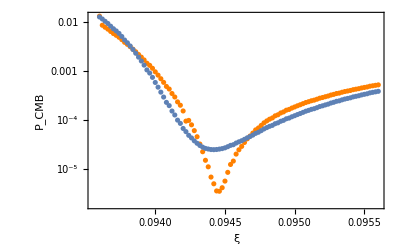

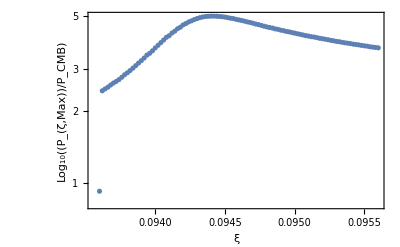

```mathematica
(*Here are the plots about the scan over ξ*)
plot = ListLogPlot[CMB,Frame->True,FrameLabel->{"ξ",Subscript[P,"CMB"]},FrameStyle->Black(*,Joined->True*)];
plotbis = ListLogPlot[ExCMB,PlotStyle->Orange,(*Joined->True,*)Frame->True,FrameLabel->{"ξ",Subscript[P,"CMB"]},FrameStyle->Black];
plot2 = ListLogPlot[Dat,Frame->True,FrameLabel->{"ξ",Subscript[Log,10][Subscript[P,"ζ,Max"]/Subscript[P,"CMB"]]},FrameStyle->Black(*,Joined->True*)];
Show[plotbis,plot]
Show[plot2]
```

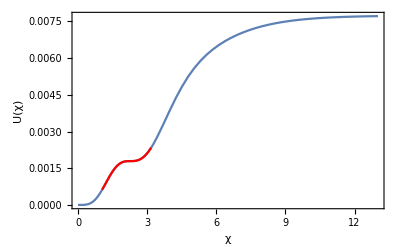

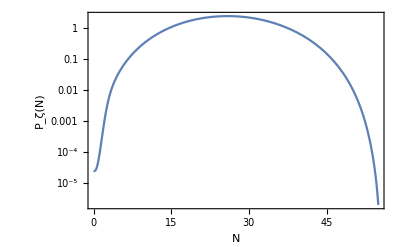

```mathematica
(*Here are the plots about the minimal CMB at some given yt0*)
(*First, we find the rank of the minimal CMB and extract the corresponding parameters from the tables.*)
ExCMBValue = {};
For[i=1,i<=Length[ExCMB],i++, AppendTo[ExCMBValue,ExCMB[[i]][[2]]]];
For[i=1,i<=Length[ExCMB],i++, If[ExCMBValue[[i]]==Min[ExCMBValue],Rank = i;]];
ξ = ExCMB[[Rank]][[1]]; δλ = Lam[[Rank]][[2]];
(*Then, we repeat the inflationary analysis to get the trajectory (red curve).*)
χi = 4/Sqrt[ξ]; L = 1000/Sqrt[ξ];
dχi = -Sqrt[2ϵSR[χi,ξ,δλ]];
χsol =NDSolveValue[{y''[Ne] + 3 y'[Ne] -1/2 (y'[Ne])^3 + (3-1/2(y'[Ne])^2)dU[y[Ne],ξ,δλ]/U[y[Ne],ξ,δλ]==0,y[0]==χi, y'[0]==dχi},y,{Ne,$MachineEpsilon,L}];
Nup = ResourceFunction["InterpolatingFunctionDomain"][χsol][[1]][[2]];
ϵ[x1_]= 1/2(χsol'[x1])^2;
H[x1_]=Sqrt[U[χsol[x1],ξ,δλ]/(6-(χsol'[x1])^2)];
Δ = Abs[Nup -55];
T =If[Δ < 5, Table[{ϵ[x]-1,x},{x,Nup-Δ,Nup,0.001}],Table[{ϵ[x]-1,x},{x,Nup-Δ,Nup,0.005}]];
Laste = False;
For[a =1, a<=Length[T]-1, a++, 
If[Laste == False,If[Sign[T[[a]][[1]]]!= Sign[T[[a+1]][[1]]],A = a; Laste = True]]
];
Nend = T[[A]][[2]];
NCMB = Nend-55;
Pζ[Nfold_]= H[Nfold]^2/(8 Pi^2 ϵ[Nfold]);
plot3 = Plot[U[x,ξ,δλ],{x,0,4/Sqrt[ξ]},FrameLabel->{"χ",U[χ]},Frame->True,LabelStyle->{Black}];
plot4 = Plot[U[x,ξ,δλ],{x,Re[χsol[NCMB]],Re[χsol[Nend]]},PlotStyle->Red];
plot5 = LogPlot[Pζ[x+NCMB],{x,0,55},FrameLabel->{"N",Subscript[P,ζ]["N"]},Frame->True,LabelStyle->{Black}];
plot5 = LogPlot[Pζ[x+NCMB],{x,0,55},FrameLabel->{"N",Subscript[P,ζ]["N"]},Frame->True,LabelStyle->{Black}];
Show[plot3,plot4]
Show[plot5]
```